```mathematica
MNIST Data fetch
```

```mathematica
prepareData[]:= Module[{tx, tt, ty,txT, ttT, tyT, i, training, testing}, 
training = RandomSample[ExampleData[{"MachineLearning","MNIST"},"TrainingData"]];
testing = RandomSample[ExampleData[{"MachineLearning", "MNIST"}, "TestData"]];
txT = ArrayReshape[Map[ImageData, testing[[;;, 1]]], {10000, 784}];
ttT = testing[[;;, 2]];
tyT = ConstantArray[0, {10000, 10}];
For[i = 1, i≤10000, i++, tyT[[i, 1+ttT[[i]]]] = 1;];
tx = ArrayReshape[Map[ImageData, training[[;;, 1]]], {60000, 784}];
tt  = training[[;;, 2]];
ty = ConstantArray[0, {60000, 10}];
For[i = 1, i≤60000, i++, ty[[i, 1+tt[[i]]]] = 1;]; Return[{tx, ty, txT, tyT}];];
{input, target, testinp, testtar} = prepareData[];
```

```mathematica
Xavier Initialization of network
```

```mathematica
initializeWeights[hiddennodes1_, hiddennodes2_, outputnodes_] := Module[{mininet, netinit, w0, w1, w2},
mininet = NetChain[{LinearLayer[hiddennodes1], Ramp,LinearLayer[hiddennodes2], Ramp, LinearLayer[outputnodes], LogisticSigmoid}, "Input"->784];
netinit = NetInitialize[mininet, Method ->{"Xavier"}];
w0 = Transpose@NetExtract[netinit, {All, "Weights"}][[1]];
w1 = Transpose@NetExtract[netinit, {All, "Weights"}][[3]];
w2 = Transpose@NetExtract[netinit, {All, "Weights"}][[5]];
Return[{w0, w1, w2}];];
```

```mathematica
Define network variables
```

```mathematica
learningrate = 0.0003;
hiddennodes1 = 128;
hiddennodes2 = 128;
outputnodes = 10;
batchsize = 16;
iterations = Floor[60000/batchsize];
epochs = 20;
b1 = 0.9;
b2 = 0.999;
epsilon = 0.00000001;
inputdim  = 784;
```

```mathematica
Binarization functions
```

```mathematica
bGradForward[x_] := Return[Max[Abs[Flatten[x]]]*Sign[x]];
bForward[x_] := Return[Mean[Abs[Flatten[x]]]*Sign[x]];
bBackward[x_] := Return[Clip[x, {-1, 1}, {0, 0}]];
```

```mathematica
kk = RandomVariate[NormalDistribution[], {784, 128}];
```

```mathematica
Timing[bBackward[kk]][[1]]
```

0.015625

```mathematica
k = RandomVariate[NormalDistribution[], {5, 6}];
MatrixForm[bForward[bForward[k]]]
MatrixForm[bBackward@k]
```

(0.738821 | 0.738821 | 0.738821 | -0.738821 | 0.738821 | -0.738821
-0.738821 | -0.738821 | -0.738821 | 0.738821 | -0.738821 | -0.738821
0.738821 | -0.738821 | -0.738821 | -0.738821 | 0.738821 | -0.738821
-0.738821 | -0.738821 | 0.738821 | -0.738821 | 0.738821 | -0.738821
0.738821 | -0.738821 | -0.738821 | -0.738821 | 0.738821 | -0.738821)

(0.0832885 | 0.199097 | 0.361828 | -0.477876 | 0.506236 | 0.
0. | -0.696917 | -0.127833 | 0.535613 | -0.155836 | -0.496212
0.351485 | 0. | -0.970229 | -0.37551 | 0.775716 | 0.
-0.793314 | -0.0677484 | 0.533873 | 0. | 0.84331 | 0.
0.684809 | 0. | 0. | -0.0466625 | 0.87104 | -0.0198331)

```mathematica
Derivative functions
```

```mathematica
sigmDeriv[x_] := Return[x*(1-x)];
rampDeriv[x_] := Return[UnitStep[x]];
```

```mathematica
Layer evaluator function
```

```mathematica
layerEval[x_, layer_Association]:=layerEval[x, Lookup[layer, "LayerType"], Lookup[layer,"Parameters"]];
layerEval[x_, "Sigmoid", param_]:= 1/(1+Exp[-x]);
layerEval[x_, "Ramp", param_] := Abs[x]*UnitStep[x];
layerEval[ x_, "LinearLayer", param_]:= Dot[x, param["Weights"]];
layerEval[ x_, "BinLayer", param_]:= Dot[bForward[x], bForward[param["Weights"]]];
layerEval[x_, "BinarizeLayer", param_]:= bForward[x];
netEvaluate[net_, x_, "Training"] := FoldList[layerEval, x, net];
netEvaluate[net_, x_, "Test"] := Fold[layerEval, x, net];
```

```mathematica
Test network unrolling
```

```mathematica
(* Define net weights *)
net={<|"LayerType"->"LinearLayer", "Parameters"-><|"Weights" -> w0|>|>,
<|"LayerType"->"Ramp"|>,
 <|"LayerType"->"BinarizeLayer"|>,
<|"LayerType"->"BinLayer", "Parameters"-><|"Weights"->w1|>|>, 
<|"LayerType"->"Ramp"|>,
<|"LayerType"->"LinearLayer", "Parameters"-><|"Weights"->w2|>|>, 
 <|"LayerType"->"Sigmoid"|>
};
iteration = 5;
```

```mathematica
fullnet = netEvaluate[net, input[[iteration;;iteration+batchsize]], "Training"];
```

```mathematica
l3Error = fullnet[[-1]] - target[[iteration;;iteration+batchsize]];
l3Delta = l3Error*sigmDeriv[fullnet[[-1]]];
l2Error = hbBackward[Dot[l3Delta, Transpose@hbWForward[w2]]];
l2Delta = l2Error*rampDeriv[fullnet[[6]]];
l1Error = hbBackward[Dot[l2Delta, Transpose@hbWForward[w1]]];l1Delta = l1Error*rampDeriv[fullnet[[3]]];
```

```mathematica
l2Delta[[;;,2]]
```

{1}
 |  |  |  |

```mathematica
Dimensions@fullnet
```

{8,17}

```mathematica
Back Propagation algorithm : EASY
```

```mathematica
backProp[fullnet_, w0_, w1_, w2_, input_, target_, l3M_, l3V_,  l2M_, l1M_, l2V_, l1V_ , iteration_]:=Module[{l3Error, l3Delta, l2Error, l2Delta, l1Error, l1Delta, g2, g1, g0, l0, l1, l2, l3, l1MC, l1VC, l2MC, l2VC, l3MC, l3VC, l3MT, l2MT, l1MT, l3VT, l2VT, l1VT, w2T, w1T, w0T, w2UDT,  w1UDT, w0UDT},

l3MT = l3M; l3VT = l3V; 
l2MT = l2M; l2VT = l2V;
l1MT = l1M; l1VT = l1V;
w2T = w2; w1T = w1; w0T = w0;

(*l3Error = fullnet[[-1]] - target;
l3Delta = l3Error*sigmDeriv[fullnet[[9]]];
l2Error = Dot[bGradForward[l3Delta], Transpose@bForward[w2]];
l2Delta = l2Error*rampDeriv[fullnet[[6]]];
l1Error = Dot[bGradForward[l2Delta], Transpose@bForward[w1]];
l1Delta = l1Error*rampDeriv[fullnet[[3]]];

g2 = Dot[Transpose[fullnet[[7]]], bGradForward[l3Delta]];
g1 = Dot[Transpose[fullnet[[4]]], bGradForward[l2Delta]];
g0 = Dot[Transpose[input], l1Delta];

l3MT = l3MT*b1 + (1-b1)*g2;
l3VT = l3VT*b2 + (1-b2)*(g2*g2);
l2MT = l2MT*b1 + (1-b1)*g1;
l2VT = l2VT*b2 + (1-b2)*(g1*g1);
l1MT = l1MT*b1 + (1-b1)*g0;
l1VT = l1VT*b2 + (1-b2)*(g0*g0);

l1MC = l1MT/(1-b1^iteration); l1VC = l1VT/(1-b2^iteration); 
l2MC = l2MT/(1-b1^iteration); l2VC = l2VT/(1-b2^iteration); 
l3MC = l3MT/(1-b1^iteration); l3VC = l3VT/(1-b2^iteration); 

w2UDT = l3MC/(Sqrt[l3VC + epsilon]);
w1UDT = l2MC/(Sqrt[l2VC + epsilon]);
w0UDT = l1MC/(Sqrt[l1VC + epsilon]); 

w2T -= learningrate*w2UDT;
w1T -= learningrate*w1UDT;
w0T -= learningrate*w0UDT; 
*)

l3Error = fullnet[[-1]] - target;
l3Delta = l3Error*sigmDeriv[fullnet[[-1]]];
l2Error =Dot[l3Delta, Transpose[w2]];
l2Delta = l2Error*rampDeriv[fullnet[[6]]];
l1Error =Dot[l2Delta, Transpose[w1]];
l1Delta = l1Error*rampDeriv[fullnet[[3]]];
g2 = Dot[Transpose[fullnet[[6]]], l3Delta];
g1 = Dot[Transpose[fullnet[[4]]], l2Delta];
g0 = Dot[Transpose[input], l1Delta];
l3MT = l3MT*b1 + (1-b1)*g2;
l3VT = l3VT*b2 + (1-b2)*(g2*g2);
l2MT = l2MT*b1 + (1-b1)*g1;						
l2VT = l2VT*b2 + (1-b2)*(g1*g1);
l1MT = l1MT*b1 + (1-b1)*g0;												
l1VT = l1VT*b2 + (1-b2)*(g0*g0);												
l1MC = l1MT/(1-b1^iteration); l1VC = l1VT/(1-b2^iteration);											
l2MC = l2MT/(1-b1^iteration); l2VC = l2VT/(1-b2^iteration);
l3MC = l3MT/(1-b1^iteration); l3VC = l3VT/(1-b2^iteration);
w2UDT = l3MC/(Sqrt[l3VC + epsilon]);
w1UDT =l2MC/(Sqrt[l2VC + epsilon]); w0UDT = l1MC/(Sqrt[l1VC + epsilon]);											
w2T -= learningrate*w2UDT;
w1T -= learningrate*w1UDT;													
w0T -= learningrate*w0UDT;


Return[{w0T, w1T, w2T, l3MT, l3VT, l2MT, l1MT, l2VT, l1VT}];
];
```

```mathematica
Accuracy Testing Function
```

```mathematica
test[net_, input_, target_, testnum_] := Return[{Position[netEvaluate[net, input[[testnum]], "Test"],Max[netEvaluate[net, input[[testnum]], "Test"]]] - 1,Position[target[[testnum]], 1] - 1}] 
accTest[net_, input_, target_, numTest_] := 
Module[{x, y}, y= 0;
For[x=1, x≤numTest, x++,If[Position[netEvaluate[net, input[[x]], "Test"], Max[netEvaluate[net, input[[x]], "Test"]]]==Position[target[[x]], 1] ,y++]]; Return[y/numTest]];
```

```mathematica
Network run function
```

```mathematica
runNet[input_, target_, testinp_, testtar_]:=Module[{iteration, fullnet, w0, w1, w2,l3M, l3V, l2M, l1M, l2V, l1V,
l3Error, l3Delta,l2Error, l2Delta, l1Error, l1Delta, g1, g0, l0, l1, l2,l3, l1MC, l1VC, l2MC, l2VC, l3MC, l3VC, w2UDT, w1UDT, w0UDT, epoch},

{w0, w1, w2} = initializeWeights[hiddennodes1, hiddennodes2, 10];
epoch = epochs;

l3M = 0; l3V = 0;l2M = 0; l1M = 0; l2V = 0; l1V = 0;

(* Iterator*)
For[iteration = 1, iteration≤ iterations, iteration+=batchsize,

(* If iteration ends and epoch isnt 0, reset iteration *)
If[And[iteration ≥ iterations - 32, epoch≥1], iteration=1; epoch-=1; Print["epoch "epoch];
Print["Training acc" N[accTest[net, input, target, 600]]];
Print["Test acc" N[accTest[net, testinp, testtar, 100]]];];

(* Redefine net weights *)
(* Define net weights *)
net={<|"LayerType"->"LinearLayer", "Parameters"-><|"Weights" -> w0|>|>,
<|"LayerType"->"Ramp"|>,
 <|"LayerType"->"BinarizeLayer"|>,
<|"LayerType"->"BinLayer", "Parameters"-><|"Weights"->w1|>|>, 
<|"LayerType"->"Ramp"|>,
<|"LayerType"->"LinearLayer", "Parameters"-><|"Weights"->w2|>|>, 
 <|"LayerType"->"Sigmoid"|>
};
(* Evaluate the net *)
fullnet = netEvaluate[net, input[[iteration;;iteration+batchsize]], "Training"];
(* Back prop *)
{w0, w1,w2, l3M, l3V, l2M, l1M, l2V, l1V} = backProp[fullnet, w0, w1, w2, input[[iteration;;iteration+batchsize]], target[[iteration;;iteration+batchsize]], l3M, l3V,  l2M, l1M, l2V, l1V, iteration];
];
Return[{w0, w1, w2}];]
```

```mathematica
{w0, w1, w2} = runNet[input, target, testinp, testtar];
```

19 epoch

0.165 Training acc

0.2 Test acc

18 epoch

0.495 Training acc

0.52 Test acc

17 epoch

0.641667 Training acc

0.54 Test acc

16 epoch

0.651667 Training acc

0.54 Test acc

15 epoch

0.745 Training acc

0.67 Test acc

14 epoch

0.788333 Training acc

0.72 Test acc

13 epoch

0.793333 Training acc

0.78 Test acc

12 epoch

0.83 Training acc

0.75 Test acc

11 epoch

0.836667 Training acc

0.78 Test acc

10 epoch

0.848333 Training acc

0.81 Test acc

9 epoch

0.861667 Training acc

0.81 Test acc

8 epoch

0.863333 Training acc

0.82 Test acc

7 epoch

0.865 Training acc

0.82 Test acc

6 epoch

0.866667 Training acc

0.84 Test acc

5 epoch

0.858333 Training acc

0.83 Test acc

4 epoch

0.871667 Training acc

0.83 Test acc

3 epoch

0.875 Training acc

0.81 Test acc

2 epoch

0.875 Training acc

0.82 Test acc

epoch

0.885 Training acc

0.82 Test acc

0

0.876667 Training acc

0.81 Test acc

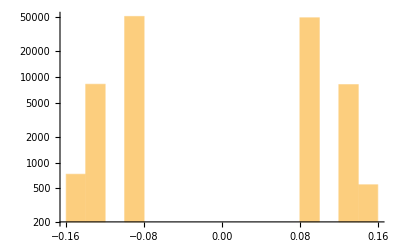

```mathematica
Histogram[Flatten[Flatten[{bForward[w1], bForward[w0], bForward[w2]}]], ScalingFunctions->"Log"]
```

```mathematica
mininet = NetChain[{LinearLayer[hiddennodes1], Ramp,LinearLayer[hiddennodes2], Ramp, LinearLayer[outputnodes], LogisticSigmoid}, "Input"->784]
```

NetChain[<>]

```mathematica
Net accuracy testing
```

```mathematica
net={<|"LayerType"->"LinearLayer","Parameters"-><|"Weights"->w0|>|>, <|"LayerType"->"Ramp"|>,<|"LayerType"->"LinearLayer","Parameters"-><|"Weights"->w1|>|>, <|"LayerType"->"Ramp"|>,<|"LayerType"->"LinearLayer","Parameters"-><|"Weights"->w2|>|>, <|"LayerType"->"Sigmoid"|>};N[accTest[net, input, target, 60000]]
N[accTest[net, testinp, testtar, 10000]]
```

```mathematica
MNIST weight saver
```

```mathematica
Export["MNISTweightsAggressive.dat", {w0, w1, w2}]
```

```mathematica
MNIST weight importer
```

```mathematica
{w0, w1, w2} = Import["MNISTweights2.dat"]
```

```mathematica
hbActForward[x_, hBL_] :=Module[{row, col,tempMat, matCreate, joinerMat, x2}, 
x2 = Transpose[x];
For[col = 1, col ≤ Dimensions[x2][[2]], col++,matCreate = Abs[ArrayReshape[x2[[;;, col]], {Ceiling[Dimensions[x2][[1]]/hBL],hBL}, 0]];
tempMat = Map[Mean, matCreate[[;;-2, ;;]], {1}];
If[Mod[Dimensions[x2][[1]], hBL]≠ 0,
AppendTo[tempMat, Total[matCreate[[-1, ;;]]]/Mod[Dimensions[x2][[1]], hBL]],
AppendTo[tempMat, Mean[matCreate[[-1, ;;]]]]];
For[row = 1, row ≤ Dimensions[x2][[1]], row++,
x2[[row, col]] = Sign[x2[[row, col]]]*tempMat[[Ceiling[row/hBL]]];
];
];
Return[Transpose[x2]]];
```

```mathematica
kk = RandomVariate[NormalDistribution[], {784, 128}];
Timing[hbActForward[kk, 4]][[1]]
```

0.5

```mathematica
Needs["CUDALink`"]
```

```mathematica
kk = RandomVariate[NormalDistribution[], {7840, 256}];
Timing[CUDADot[kk, CUDATranspose[kk]]][[1]]
Timing[Dot[kk, Transpose@kk]][[1]]
```

0.265625

0.390625

```mathematica
Timing[Dot[kk, Transpose@kk]][[1]]
```

0.